```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1
m=10
M1=√((4 L^5)/(3m))
S1=√((3m L^5)/4)
zMin=-10
zMax=10
eps=10^-3
```

1

10

√(2/15)

√(15/2)

-10

10

1/1000

```mathematica
equations={
(R'[z]Cos[b[z]]-R [z]Sin[b[z]]b'[z])/(9 (R[z]^4)^(1/3))==2/3 Log[Abs[(r[z]R[z])/L^5]],
(R'[z]Sin[b[z]]+R [z]Cos[b[z]]b'[z])/(9 (R[z]^4)^(1/3))==-2/3(a[z]+b[z]),
(r'[z]Cos[a[z]]-r [z]Sin[a[z]]a'[z])/(4Abs[r[z]])==(2R[z])/(3r[z])Cos[a[z]-b[z]]-m/2,
(r'[z]Sin[a[z]]+r [z]Cos[a[z]]a'[z])/(4Abs[r[z]])==(2R[z])/(3r[z])Sin[a[z]-b[z]]
};
```

```mathematica
bcs={
R[zMax]==1,
r[zMin]==1,
a[zMin]==eps,
b[zMax]==-Pi+eps
};
```

```mathematica
sol=NDSolve[Join[equations, bcs], {R, r, a, b}, {z, zMin, zMax}]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at z == -10..

NDSolve[{(-R[z] Sin[b[z]] b'[z]+Cos[b[z]] R'[z])/(9 (R[z]^4)^(1/3))==2/3 Log[Abs[r[z] R[z]]],(Cos[b[z]] R[z] b'[z]+Sin[b[z]] R'[z])/(9 (R[z]^4)^(1/3))==-2/3 (a[z]+b[z]),(-r[z] Sin[a[z]] a'[z]+Cos[a[z]] r'[z])/(4 Abs[r[z]])==-5+(2 Cos[a[z]-b[z]] R[z])/(3 r[z]),(Cos[a[z]] r[z] a'[z]+Sin[a[z]] r'[z])/(4 Abs[r[z]])==(2 R[z] Sin[a[z]-b[z]])/(3 r[z]),R[10]==1,r[-10]==1,a[-10]==1/1000,b[10]==1/1000-π},{R,r,a,b},{z,-10,10}]

```mathematica
solFunc=Values[sol][[1]]
Plot[{Re[solFunc[[1]][z]Exp[I*solFunc[[4]][z]]],Im[solFunc[[1]][z]Exp[I*solFunc[[4]][z]]]}, {z, zMin, -8}]
Plot[{Re[solFunc[[2]][z]Exp[I*solFunc[[3]][z]]],Im[solFunc[[2]][z]Exp[I*solFunc[[3]][z]]]}, {z, zMin, zMax}]
```

Values::invrl: The argument … is not a valid Association or a list of rules.

NDSolve[{(-R[z] Sin[b[z]] b'[z]+Cos[b[z]] R'[z])/(9 (R[z]^4)^(1/3))==2/3 Log[Abs[r[z] R[z]]],(Cos[b[z]] R[z] b'[z]+Sin[b[z]] R'[z])/(9 (R[z]^4)^(1/3))==-2/3 (a[z]+b[z]),(-r[z] Sin[a[z]] a'[z]+Cos[a[z]] r'[z])/(4 Abs[r[z]])==-5+(2 Cos[a[z]-b[z]] R[z])/(3 r[z]),(Cos[a[z]] r[z] a'[z]+Sin[a[z]] r'[z])/(4 Abs[r[z]])==(2 R[z] Sin[a[z]-b[z]])/(3 r[z]),R[10]==1,r[-10]==1,a[-10]==1/1000,b[10]==1/1000-π},{R,r,a,b},{z,-10,10}]

NDSolve::dsvar: -9.99996 cannot be used as a variable.

Part::partw: Part 4 of NDSolve[«1»] does not exist.

NDSolve::dsvar: -9.99996 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

Part::partw: Part 4 of NDSolve[«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

NDSolve::dsvar: -9.99959 cannot be used as a variable.

NDSolve::dsvar: -9.59143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{solFunc[[1]][z],solFunc[[2]][z],solFunc[[3]][z],solFunc[[4]][z]},{z, zMin, -9.9}, PlotLegends->{"R","r","a","b"}]
```

InterpolatingFunction::dmval: Input value {-10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
solFunc[[3]][-8]
```

InterpolatingFunction::dmval: Input value {-8} lies outside the range of data in the interpolating function. Extrapolation will be used.

-2.30294×10^33

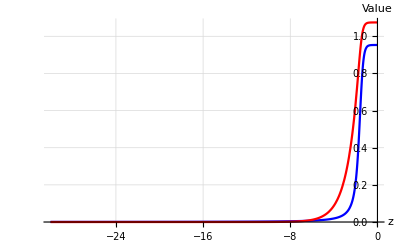

```mathematica
(*Parameters*)mHat=1;
perturb=10^-5;(*Small perturbation*)(*Fixed point calculation*)phiFixed=(3/4)^(1/6);
chiFixed=Sqrt[4/3*phiFixed^3];

(*Perturbed initial conditions at z=0*)
startPhi=phiFixed*(1-perturb);
startChi=chiFixed*(1-perturb);

(*System of ODEs*)
eqns={phi'[z]==-2*mHat^(1/6)*phi[z]^2*Log[phi[z]^3*chi[z]^2],chi'[z]==mHat*chi[z]*(1-(4*phi[z]^3)/(3*chi[z]^2)),phi[0]==startPhi,chi[0]==startChi};

(*Solve ODE backward from z=0 to z=-30*)
sol=NDSolve[eqns,{phi,chi},{z,-30,0},Method->"StiffnessSwitching",(*Handles potential stiffness*)WorkingPrecision->25,(*Higher precision for stability*)MaxSteps->100000              (*Allow sufficient steps*)];

(*Plot the solution*)
Plot[Evaluate[{phi[z],chi[z]}/. sol],{z,-30,0},PlotRange->All,AxesLabel->{"z","Value"},PlotStyle->{Blue,Red},GridLines->Automatic]
```

```mathematica
ClearAll["Global`*"]
```

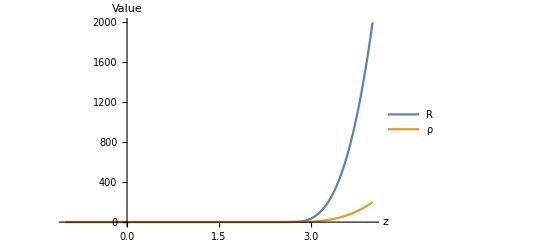

```mathematica
(*Parameters*)m=4/3;(*Must be 4/3 for equilibrium at z->-∞*)epsilon=1*^-10;(*Small perturbation magnitude*)z0=-1;(*Starting point (not too negative)*)(*Compute eigenvalues and eigenvectors*)sqrt313=Sqrt[313];
lambda1=(5+sqrt313)/3;(*Unstable eigenvalue~7.56*)lambda2=(-5+sqrt313)/3;(*Unstable eigenvalue~4.23*)(*Eigenvector for lambda1 (R-ρ subsystem)*)v1R=1;
v1ρ=(lambda1-6)/6;(* ~0.261*)(*Eigenvector for lambda2 (α-β subsystem)*)v2β=1;
v2α=(-6-lambda2)/6;(* ~-0.586*)(*Asymptotic expansion at z=z0*)R0=1+epsilon*v1R*Exp[lambda1*z0];
ρ0=1+epsilon*v1ρ*Exp[lambda1*z0];
α0=0+epsilon*v2α*Exp[lambda2*z0];
β0=0+epsilon*v2β*Exp[lambda2*z0];

(*Regularized ODE system with safeguards*)
ρRmin=1*^-15;(*Prevents log(0)*)odes={R'[z]==6 R[z]^(4/3) (Log[Max[ρRmin,Abs[ρ[z] R[z]]]] Cos[β[z]]-(α[z]+β[z]) Sin[β[z]]),β'[z]==-6 R[z]^(1/3) (Log[Max[ρRmin,Abs[ρ[z] R[z]]]] Sin[β[z]]+(α[z]+β[z]) Cos[β[z]]),ρ'[z]==(8/3 R[z] Cos[α[z]-β[z]]-2 m ρ[z]) Cos[α[z]]+8/3 R[z] Sin[α[z]-β[z]] Sin[α[z]],α'[z]==(1/ρ[z])*(-(8/3 R[z] Cos[α[z]-β[z]]-2 m ρ[z]) Sin[α[z]]+8/3 R[z] Sin[α[z]-β[z]] Cos[α[z]]),R[z0]==R0,ρ[z0]==ρ0,α[z0]==α0,β[z0]==β0
};

(*Solve with high-precision stiff solver*)
sol=NDSolve[odes,{R,ρ,α,β},{z,z0,2.7},Method->{"BDF"},WorkingPrecision->30,(*Arbitrary precision*)MaxSteps->100000,PrecisionGoal->10,AccuracyGoal->12];

(*Plot solutions*)
Plot[Evaluate[{R[z],ρ[z]}/. sol],{z,z0,4},PlotLegends->{"R","ρ","α","β"},AxesLabel->{"z","Value"},PlotRange->All]
```